# Cascade Spectra

### This file describes the contents of the “Spectra” directory and further below examples of how to load them into Mathematica

Supplementary material for G. Elor, N. Rodd, T. Slatyer, W. Xue, “Model-Independent Indirect Detection Constraints on Hidden Sector Dark Matter” (2015)
Contact: Nick Rodd <nrodd@mit.edu>

Overview: Files within “Spectra” contain the γ, e^+/e^- and p spectrum of dark matter (DM) annihilations leading to 1-6 step cascades ending in e, μ, τ, b-quark, W, h or gluon final states. A separate .dat file is provided for each type of spectrum and final state. Note all spectra here are calculated using the large hierarchy approximation, which can break down in certain situations. The contents of these files are designed to be similar to the results of M. Cirelli et al., JCAP 1103, 051 (2011), 1012.4515.

Mathematica version details: this file was written in Mathematica 10. It runs fine (but with some harmless error messages) in Mathematica 9. Due to the use of the PlotLegends function, it will not operate with Mathematica 8, but if these are deleted the files will run.

Content of files: There are 18 files of the form Cascade_{Final State}_{Spectrum Type}.dat. Each contains 8 columns and 1612 rows (the first row contains the column labels and all others contain numerical values). For all files except gluon final states and the positron spectrum from gammas, the columns are: 
1. ϵ_f value; 
2. Log_10[x], where x=E/m_DM; 
3-8. the value of dN/(dLog_10(x))=ln(10)x dN/dx of an n=1 (column 3) up to n=6 (column 8) spectrum at that value of ϵ_f and x. 
For final state gluons and the positron spectrum from gammas, the columns are:
1. m_ϕ value; 
2. Log_10[x], where x=E/m_DM; 
3-8. the value of dN/(dLog_10(x))=ln(10)x dN/dx of an n=1 (column 3) up to n=6 (column 8) spectrum at that value of m_ϕ and x. 
The reason for this difference in the case of gluons and the positron spectrum from gammas is that we have to use m_ϕ values instead of ϵ_f=2m_f/m_ϕ as for these final states m_f=0 making ϵ_f less useful.

Range of parameters: Log_10[x] ranges from -8.9 to 0 in steps on 0.05, covering the entire range where x^2 dN/dx for each spectra is non-zero. ϵ_f is evaluated at 0.01, 0.03, 0.05, 0.07, 0.1, 0.2, 0.3, 0.4 and 0.5, whilst m_ϕ is given at 10, 20, 40, 50, 80, 100, 500, 1000 and 2000 GeV.
NB: if using a value of ϵ_f or m_ϕ not in this list - especially if it is outside the range of values provided - it is recommended that linear interpolation be used, as described in the examples below.
NB: as we are using an interpolating function to determine the spectrum, it can occasionally go negative. This is unphysical can cause issues if the Log of the spectrum is being used, and so we set the spectrum to 0 wherever the interpolating function would send it negative.

Brief description of files
Photon Spectra:
Cascade_{Gam,E,Mu,Tau,B,W,H,G}_gammas.dat - photon spectrum from final state {photons, electrons, muons, taus, b-quarks, Ws, Higgs, gluons}

Positron/Electron Spectra:
Cascade_{Gam,E,Mu,Tau,B,W,H,G}_positrons.dat - positron (or equivalently electron) spectrum from final state {photons, electrons, muons, taus, b-quarks, Ws, Higgs, gluons}

Antiproton Spectra:
Cascade_{B,W,H,G}_antiprotons.dat - antiproton spectrum from final state {b-quarks, Ws, Higgs, gluons}
NB: electron, muon and tau antiproton spectra are negligible and so not given

Direct Spectra:
AtProduction_{gammas,positrons,antiprotons}.dat - Direct {photon, positron, antiproton} spectrum as calculated by M. Cirelli et al. These files were produced by those authors, but we provide them here for convenience.

## Photon Cascade Spectra of Final State W Bosons for ϵ_f=0.1

In this example we load the photon spectrums of 1-6 step cascade DM annihilations terminating in W bosons for ϵ_f=0.1.

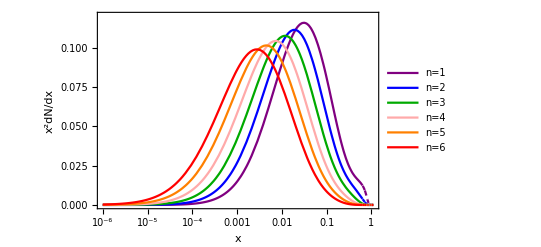

```mathematica
Clear[BaseDir,load,ϵvals,ϵ,xvals,flux,loadspec1,loadspec2,loadspec3,loadspec4,loadspec5,loadspec6,dNdx1,dNdx2,dNdx3,dNdx4,dNdx5,dNdx6]
BaseDir=NotebookDirectory[];
load=Import[BaseDir<>"Spectra/Cascade_W_gammas.dat"];
ϵvals=load[[2;;Dimensions[load][[1]],1]];
ϵ=0.1;
xvals=10^(load[[2;;Dimensions[load][[1]],2]]);
flux=(1/(Log[10]xvals))load[[2;;Dimensions[load][[1]],3]];
loadspec1=Interpolation[Table[{{ϵvals[[i]],xvals[[i]]},flux[[i]]},{i,Dimensions[load][[1]]-1}]];
dNdx1[x_]=Piecewise[{{If[loadspec1[ϵ,x]>0,loadspec1[ϵ,x],0],x≤1},{0,x>1}}];
flux=(1/(Log[10]xvals))load[[2;;Dimensions[load][[1]],4]];
loadspec2=Interpolation[Table[{{ϵvals[[i]],xvals[[i]]},flux[[i]]},{i,Dimensions[load][[1]]-1}]];
dNdx2[x_]=Piecewise[{{If[loadspec2[ϵ,x]>0,loadspec2[ϵ,x],0],x≤1},{0,x>1}}];
flux=(1/(Log[10]xvals))load[[2;;Dimensions[load][[1]],5]];
loadspec3=Interpolation[Table[{{ϵvals[[i]],xvals[[i]]},flux[[i]]},{i,Dimensions[load][[1]]-1}]];
dNdx3[x_]=Piecewise[{{If[loadspec3[ϵ,x]>0,loadspec3[ϵ,x],0],x≤1},{0,x>1}}];
flux=(1/(Log[10]xvals))load[[2;;Dimensions[load][[1]],6]];
loadspec4=Interpolation[Table[{{ϵvals[[i]],xvals[[i]]},flux[[i]]},{i,Dimensions[load][[1]]-1}]];
dNdx4[x_]=Piecewise[{{If[loadspec4[ϵ,x]>0,loadspec4[ϵ,x],0],x≤1},{0,x>1}}];
flux=(1/(Log[10]xvals))load[[2;;Dimensions[load][[1]],7]];
loadspec5=Interpolation[Table[{{ϵvals[[i]],xvals[[i]]},flux[[i]]},{i,Dimensions[load][[1]]-1}]];
dNdx5[x_]=Piecewise[{{If[loadspec5[ϵ,x]>0,loadspec5[ϵ,x],0],x≤1},{0,x>1}}];
flux=(1/(Log[10]xvals))load[[2;;Dimensions[load][[1]],8]];
loadspec6=Interpolation[Table[{{ϵvals[[i]],xvals[[i]]},flux[[i]]},{i,Dimensions[load][[1]]-1}]];
dNdx6[x_]=Piecewise[{{If[loadspec6[ϵ,x]>0,loadspec6[ϵ,x],0],x≤1},{0,x>1}}];
LogLinearPlot[{x^2 dNdx1[x],x^2 dNdx2[x],x^2 dNdx3[x],x^2 dNdx4[x],x^2 dNdx5[x],x^2 dNdx6[x]},{x,10^-6,1.1},PlotRange->{{10^-6,1.1},{0,0.12}},Frame-> True, FrameLabel-> {"x","x^2dN/dx "},Axes-> False,PlotStyle-> {Purple,Blue,Darker[Green],Lighter[Pink],Orange,Red},PlotLegends->{"n=1","n=2","n=3","n=4","n=5","n=6"}]
```

## Positron Cascade Spectra of Final State b-quarks for ϵ_f=0.06

In this example we load the positron spectrums of 1-6 step cascade step DM annihilations terminating in b-quarks for ϵ_f=0.06. As this value of ϵ_f isn’t one of those provided, we use linear interpolation to get to this value, which results in a slightly bumpy spectrum.

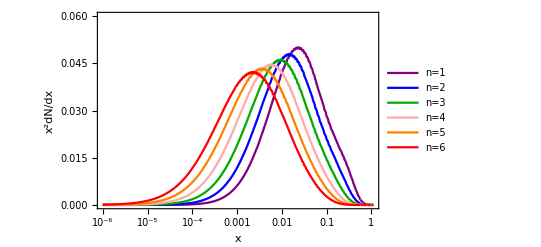

```mathematica
Clear[BaseDir,load,ϵvals,ϵ,xvals,flux,loadspec1,loadspec2,loadspec3,loadspec4,loadspec5,loadspec6,dNdx1,dNdx2,dNdx3,dNdx4,dNdx5,dNdx6]
BaseDir=NotebookDirectory[];
load=Import[BaseDir<>"Spectra/Cascade_B_positrons.dat"];
ϵvals=load[[2;;Dimensions[load][[1]],1]];
ϵ=0.06;
xvals=10^(load[[2;;Dimensions[load][[1]],2]]);
flux=(1/(Log[10]xvals))load[[2;;Dimensions[load][[1]],3]];
loadspec1=Interpolation[Table[{{ϵvals[[i]],xvals[[i]]},flux[[i]]},{i,Dimensions[load][[1]]-1}],InterpolationOrder->1];
dNdx1[x_]=Piecewise[{{If[loadspec1[ϵ,x]>0,loadspec1[ϵ,x],0],x≤1},{0,x>1}}];
flux=(1/(Log[10]xvals))load[[2;;Dimensions[load][[1]],4]];
loadspec2=Interpolation[Table[{{ϵvals[[i]],xvals[[i]]},flux[[i]]},{i,Dimensions[load][[1]]-1}],InterpolationOrder->1];
dNdx2[x_]=Piecewise[{{If[loadspec2[ϵ,x]>0,loadspec2[ϵ,x],0],x≤1},{0,x>1}}];
flux=(1/(Log[10]xvals))load[[2;;Dimensions[load][[1]],5]];
loadspec3=Interpolation[Table[{{ϵvals[[i]],xvals[[i]]},flux[[i]]},{i,Dimensions[load][[1]]-1}],InterpolationOrder->1];
dNdx3[x_]=Piecewise[{{If[loadspec3[ϵ,x]>0,loadspec3[ϵ,x],0],x≤1},{0,x>1}}];
flux=(1/(Log[10]xvals))load[[2;;Dimensions[load][[1]],6]];
loadspec4=Interpolation[Table[{{ϵvals[[i]],xvals[[i]]},flux[[i]]},{i,Dimensions[load][[1]]-1}],InterpolationOrder->1];
dNdx4[x_]=Piecewise[{{If[loadspec4[ϵ,x]>0,loadspec4[ϵ,x],0],x≤1},{0,x>1}}];
flux=(1/(Log[10]xvals))load[[2;;Dimensions[load][[1]],7]];
loadspec5=Interpolation[Table[{{ϵvals[[i]],xvals[[i]]},flux[[i]]},{i,Dimensions[load][[1]]-1}],InterpolationOrder->1];
dNdx5[x_]=Piecewise[{{If[loadspec5[ϵ,x]>0,loadspec5[ϵ,x],0],x≤1},{0,x>1}}];
flux=(1/(Log[10]xvals))load[[2;;Dimensions[load][[1]],8]];
loadspec6=Interpolation[Table[{{ϵvals[[i]],xvals[[i]]},flux[[i]]},{i,Dimensions[load][[1]]-1}],InterpolationOrder->1];
dNdx6[x_]=Piecewise[{{If[loadspec6[ϵ,x]>0,loadspec6[ϵ,x],0],x≤1},{0,x>1}}];
LogLinearPlot[{x^2 dNdx1[x],x^2 dNdx2[x],x^2 dNdx3[x],x^2 dNdx4[x],x^2 dNdx5[x],x^2 dNdx6[x]},{x,10^-6,1.1},PlotRange->{{10^-6,1.1},{0,0.06}},Frame-> True, FrameLabel-> {"x","x^2dN/dx "},Axes-> False,PlotStyle-> {Purple,Blue,Darker[Green],Lighter[Pink],Orange,Red},PlotLegends->{"n=1","n=2","n=3","n=4","n=5","n=6"}]
```

## Antiproton Cascade Spectra of Final State Gluons for m_ϕ=50 GeV

In this example we load the antiproton spectrums of 1-6 step cascade step DM annihilations terminating in gluons for m_ϕ=50 GeV.

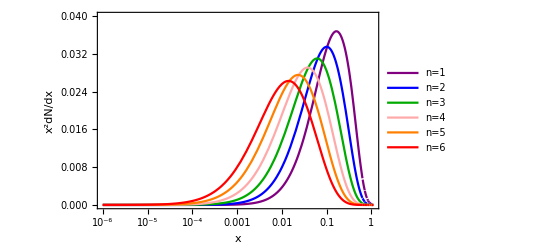

```mathematica
Clear[BaseDir,load,mϕvals,mϕ,xvals,flux,loadspec1,loadspec2,loadspec3,loadspec4,loadspec5,loadspec6,dNdx1,dNdx2,dNdx3,dNdx4,dNdx5,dNdx6]
BaseDir=NotebookDirectory[];
load=Import[BaseDir<>"Spectra/Cascade_G_antiprotons.dat"];
mϕvals=load[[2;;Dimensions[load][[1]],1]];
mϕ=50;
xvals=10^(load[[2;;Dimensions[load][[1]],2]]);
flux=(1/(Log[10]xvals))load[[2;;Dimensions[load][[1]],3]];
loadspec1=Interpolation[Table[{{mϕvals[[i]],xvals[[i]]},flux[[i]]},{i,Dimensions[load][[1]]-1}]];
dNdx1[x_]=Piecewise[{{If[loadspec1[mϕ,x]>0,loadspec1[mϕ,x],0],x≤1},{0,x>1}}];
flux=(1/(Log[10]xvals))load[[2;;Dimensions[load][[1]],4]];
loadspec2=Interpolation[Table[{{mϕvals[[i]],xvals[[i]]},flux[[i]]},{i,Dimensions[load][[1]]-1}]];
dNdx2[x_]=Piecewise[{{If[loadspec2[mϕ,x]>0,loadspec2[mϕ,x],0],x≤1},{0,x>1}}];
flux=(1/(Log[10]xvals))load[[2;;Dimensions[load][[1]],5]];
loadspec3=Interpolation[Table[{{mϕvals[[i]],xvals[[i]]},flux[[i]]},{i,Dimensions[load][[1]]-1}]];
dNdx3[x_]=Piecewise[{{If[loadspec3[mϕ,x]>0,loadspec3[mϕ,x],0],x≤1},{0,x>1}}];
flux=(1/(Log[10]xvals))load[[2;;Dimensions[load][[1]],6]];
loadspec4=Interpolation[Table[{{mϕvals[[i]],xvals[[i]]},flux[[i]]},{i,Dimensions[load][[1]]-1}]];
dNdx4[x_]=Piecewise[{{If[loadspec4[mϕ,x]>0,loadspec4[mϕ,x],0],x≤1},{0,x>1}}];
flux=(1/(Log[10]xvals))load[[2;;Dimensions[load][[1]],7]];
loadspec5=Interpolation[Table[{{mϕvals[[i]],xvals[[i]]},flux[[i]]},{i,Dimensions[load][[1]]-1}]];
dNdx5[x_]=Piecewise[{{If[loadspec5[mϕ,x]>0,loadspec5[mϕ,x],0],x≤1},{0,x>1}}];
flux=(1/(Log[10]xvals))load[[2;;Dimensions[load][[1]],8]];
loadspec6=Interpolation[Table[{{mϕvals[[i]],xvals[[i]]},flux[[i]]},{i,Dimensions[load][[1]]-1}]];
dNdx6[x_]=Piecewise[{{If[loadspec6[mϕ,x]>0,loadspec6[mϕ,x],0],x≤1},{0,x>1}}];
LogLinearPlot[{x^2 dNdx1[x],x^2 dNdx2[x],x^2 dNdx3[x],x^2 dNdx4[x],x^2 dNdx5[x],x^2 dNdx6[x]},{x,10^-6,1.1},PlotRange->{{10^-6,1.1},{0,0.04}},Frame-> True, FrameLabel-> {"x","x^2dN/dx "},Axes-> False,PlotStyle-> {Purple,Blue,Darker[Green],Lighter[Pink],Orange,Red},PlotLegends->{"n=1","n=2","n=3","n=4","n=5","n=6"}]
```

## Positron Direct Spectrum of Final State b-quarks for ϵ_f=0.3

In this example we load the 0-step positron spectrum for a DM annihilation proceeding directly  into b-quarks for ϵ_f=0.3. For other final states, replace the 14 in the flux row with: 5 (electrons), 8 (muons), 11 (taus), 14 (b-quarks), 18 (W bosons), 22 (gluons), 23 (photons) or 24 (Higgs).
Note for certain direct spectra, like the positron spectrum from final state electrons, or the photon spectrum from final state photons, the spectrum is actually a Dirac δ-function and it may often be easier to just use this analytic expression.

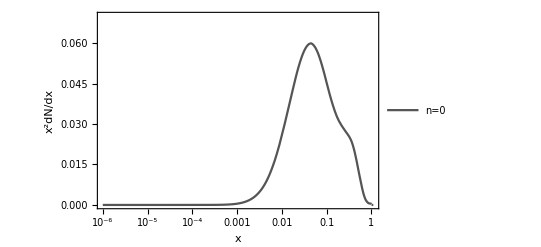

```mathematica
Clear[BaseDir,load,mf,mass,xval,flux,loadspec,dNdx0]
BaseDir=NotebookDirectory[];
load=Import[BaseDir<>"Spectra/AtProduction_positrons.dat"];
mf=4.18;
ϵ=0.3;
mass=load[[2;;Dimensions[load][[1]],1]]; (*in GeV*)
xval=10^(load[[2;;Dimensions[load][[1]],2]]); (*x = E/M*)
flux=(1/(Log[10]xval))load[[2;;Dimensions[load][[1]],14]];
loadspec=Interpolation[Table[{{mass[[i]],xval[[i]]},flux[[i]]},{i,Dimensions[load][[1]]-1}]];
dNdx0[x_]=Piecewise[{{loadspec[mf/ϵ,x],x≤1},{0,x>1}}];
LogLinearPlot[{x^2 dNdx0[x]},{x,10^-6,1.1},PlotRange->{{10^-6,1.1},{0,0.07}},Frame-> True, FrameLabel-> {"x","x^2dN/dx "},Axes-> False,PlotStyle-> {Darker[Gray]},PlotLegends->{"n=0"}]
```

NB: recall ϵ=mf/m_χ, so above when we specified ϵ and subbed in mf/ϵ, we could equally well have specified m_χ and subbed it in. An example of this is shown below

## Photon Direct Spectrum of Final State gluons for m_χ=25 GeV

In this example we load the 0-step photon spectrum for a DM annihilation proceeding directly  into gluons for m_χ=25 GeV. This is an alternative to loading via specifying ϵ or m_ϕ (the latter being appropriate for gluons). Note for a direct spectrum m_ϕ=2 m_χ, so specifying one fixes the other. See the previous example for further details.

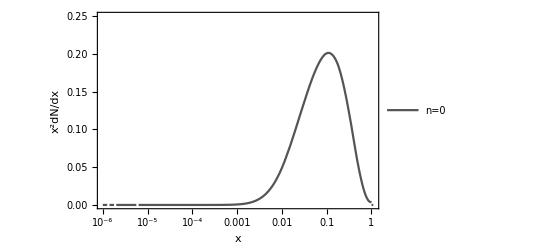

```mathematica
Clear[BaseDir,load,mf,mass,xval,flux,loadspec,dNdx0]
BaseDir=NotebookDirectory[];
load=Import[BaseDir<>"Spectra/AtProduction_gammas.dat"];
mχ=25;
mass=load[[2;;Dimensions[load][[1]],1]]; (*in GeV*)
xval=10^(load[[2;;Dimensions[load][[1]],2]]); (*x = E/M*)
flux=(1/(Log[10]xval))load[[2;;Dimensions[load][[1]],22]];
loadspec=Interpolation[Table[{{mass[[i]],xval[[i]]},flux[[i]]},{i,Dimensions[load][[1]]-1}]];
dNdx0[x_]=Piecewise[{{loadspec[mχ,x],x≤1},{0,x>1}}];
LogLinearPlot[{x^2 dNdx0[x]},{x,10^-6,1.1},PlotRange->{{10^-6,1.1},{0,0.25}},Frame-> True, FrameLabel-> {"x","x^2dN/dx "},Axes-> False,PlotStyle-> {Darker[Gray]},PlotLegends->{"n=0"}]
```